# Omicron analysis: Plotting partitioned case counts and Rt

## Splitting out lineage BA.1 / clade 21K from lineage BA.2 / clade 21L

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us-split

```mathematica
dataset="omicron-us-split";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
gridCount=4;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron 21K","Omicron 21L"};
```

```mathematica
n=Length[variants]
```

4

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.7,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8083415999999999, 0.7110806000000001, 0.255976],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={};
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-11-01

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-02-25

```mathematica
countries=Union[seqData[[All,2]]]
```

{California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Maryland,Massachusetts,Michigan,Minnesota,New Jersey,New York,North Carolina,Ohio,Oregon,Pennsylvania,Rhode Island,Tennessee,Texas,Utah,Virginia,Washington,Wisconsin}

```mathematica
countries=Complement[countries,countriesToDrop]
```

{California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Maryland,Massachusetts,Michigan,Minnesota,New Jersey,New York,North Carolina,Ohio,Oregon,Pennsylvania,Rhode Island,Tennessee,Texas,Utah,Virginia,Washington,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->countrySequenceCounts[#][[-15;;-1]]&,countries]
```

{California→{{2022-02-11,1570},{2022-02-12,1181},{2022-02-13,691},{2022-02-14,1500},{2022-02-15,1618},{2022-02-16,2247},{2022-02-17,921},{2022-02-18,843},{2022-02-19,586},{2022-02-20,346},{2022-02-21,214},{2022-02-22,353},{2022-02-23,11},{2022-02-24,0},{2022-02-25,0}},Colorado→{{2022-02-11,325},{2022-02-12,183},{2022-02-13,118},{2022-02-14,253},{2022-02-15,277},{2022-02-16,199},{2022-02-17,79},{2022-02-18,23},{2022-02-19,15},{2022-02-20,7},{2022-02-21,28},{2022-02-22,24},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Connecticut→{{2022-02-11,77},{2022-02-12,61},{2022-02-13,67},{2022-02-14,179},{2022-02-15,220},{2022-02-16,144},{2022-02-17,171},{2022-02-18,111},{2022-02-19,44},{2022-02-20,43},{2022-02-21,136},{2022-02-22,37},{2022-02-23,18},{2022-02-24,46},{2022-02-25,27}},Florida→{{2022-02-11,274},{2022-02-12,282},{2022-02-13,248},{2022-02-14,145},{2022-02-15,186},{2022-02-16,299},{2022-02-17,251},{2022-02-18,289},{2022-02-19,189},{2022-02-20,86},{2022-02-21,81},{2022-02-22,66},{2022-02-23,5},{2022-02-24,4},{2022-02-25,0}},Georgia→{{2022-02-11,95},{2022-02-12,86},{2022-02-13,80},{2022-02-14,62},{2022-02-15,53},{2022-02-16,83},{2022-02-17,66},{2022-02-18,43},{2022-02-19,36},{2022-02-20,12},{2022-02-21,23},{2022-02-22,13},{2022-02-23,3},{2022-02-24,0},{2022-02-25,0}},Illinois→{{2022-02-11,139},{2022-02-12,119},{2022-02-13,103},{2022-02-14,168},{2022-02-15,104},{2022-02-16,88},{2022-02-17,53},{2022-02-18,75},{2022-02-19,70},{2022-02-20,60},{2022-02-21,85},{2022-02-22,50},{2022-02-23,7},{2022-02-24,3},{2022-02-25,2}},Indiana→{{2022-02-11,55},{2022-02-12,35},{2022-02-13,40},{2022-02-14,29},{2022-02-15,43},{2022-02-16,45},{2022-02-17,43},{2022-02-18,44},{2022-02-19,39},{2022-02-20,10},{2022-02-21,21},{2022-02-22,10},{2022-02-23,1},{2022-02-24,0},{2022-02-25,0}},Maryland→{{2022-02-11,40},{2022-02-12,56},{2022-02-13,51},{2022-02-14,51},{2022-02-15,40},{2022-02-16,33},{2022-02-17,35},{2022-02-18,34},{2022-02-19,17},{2022-02-20,14},{2022-02-21,13},{2022-02-22,10},{2022-02-23,1},{2022-02-24,2},{2022-02-25,0}},Massachusetts→{{2022-02-11,253},{2022-02-12,289},{2022-02-13,229},{2022-02-14,541},{2022-02-15,536},{2022-02-16,472},{2022-02-17,514},{2022-02-18,290},{2022-02-19,156},{2022-02-20,168},{2022-02-21,261},{2022-02-22,204},{2022-02-23,49},{2022-02-24,201},{2022-02-25,18}},Michigan→{{2022-02-11,79},{2022-02-12,98},{2022-02-13,55},{2022-02-14,71},{2022-02-15,96},{2022-02-16,70},{2022-02-17,58},{2022-02-18,68},{2022-02-19,56},{2022-02-20,27},{2022-02-21,43},{2022-02-22,17},{2022-02-23,0},{2022-02-24,1},{2022-02-25,0}},Minnesota→{{2022-02-11,230},{2022-02-12,141},{2022-02-13,104},{2022-02-14,135},{2022-02-15,197},{2022-02-16,177},{2022-02-17,130},{2022-02-18,117},{2022-02-19,53},{2022-02-20,66},{2022-02-21,61},{2022-02-22,58},{2022-02-23,11},{2022-02-24,1},{2022-02-25,0}},New Jersey→{{2022-02-11,115},{2022-02-12,120},{2022-02-13,77},{2022-02-14,67},{2022-02-15,38},{2022-02-16,101},{2022-02-17,112},{2022-02-18,110},{2022-02-19,57},{2022-02-20,36},{2022-02-21,31},{2022-02-22,35},{2022-02-23,1},{2022-02-24,1},{2022-02-25,0}},New York→{{2022-02-11,211},{2022-02-12,191},{2022-02-13,162},{2022-02-14,272},{2022-02-15,151},{2022-02-16,140},{2022-02-17,137},{2022-02-18,140},{2022-02-19,48},{2022-02-20,43},{2022-02-21,49},{2022-02-22,23},{2022-02-23,30},{2022-02-24,9},{2022-02-25,2}},North Carolina→{{2022-02-11,405},{2022-02-12,249},{2022-02-13,222},{2022-02-14,310},{2022-02-15,154},{2022-02-16,156},{2022-02-17,103},{2022-02-18,75},{2022-02-19,42},{2022-02-20,39},{2022-02-21,44},{2022-02-22,25},{2022-02-23,9},{2022-02-24,0},{2022-02-25,0}},Ohio→{{2022-02-11,54},{2022-02-12,19},{2022-02-13,21},{2022-02-14,41},{2022-02-15,40},{2022-02-16,34},{2022-02-17,31},{2022-02-18,20},{2022-02-19,20},{2022-02-20,9},{2022-02-21,16},{2022-02-22,16},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Oregon→{{2022-02-11,100},{2022-02-12,19},{2022-02-13,21},{2022-02-14,72},{2022-02-15,44},{2022-02-16,48},{2022-02-17,24},{2022-02-18,25},{2022-02-19,8},{2022-02-20,17},{2022-02-21,26},{2022-02-22,5},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Pennsylvania→{{2022-02-11,92},{2022-02-12,75},{2022-02-13,35},{2022-02-14,60},{2022-02-15,98},{2022-02-16,94},{2022-02-17,114},{2022-02-18,115},{2022-02-19,65},{2022-02-20,13},{2022-02-21,15},{2022-02-22,19},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Rhode Island→{{2022-02-11,25},{2022-02-12,27},{2022-02-13,11},{2022-02-14,64},{2022-02-15,54},{2022-02-16,51},{2022-02-17,40},{2022-02-18,21},{2022-02-19,3},{2022-02-20,11},{2022-02-21,29},{2022-02-22,7},{2022-02-23,10},{2022-02-24,10},{2022-02-25,0}},Tennessee→{{2022-02-11,86},{2022-02-12,76},{2022-02-13,81},{2022-02-14,55},{2022-02-15,74},{2022-02-16,59},{2022-02-17,33},{2022-02-18,43},{2022-02-19,8},{2022-02-20,8},{2022-02-21,8},{2022-02-22,17},{2022-02-23,9},{2022-02-24,0},{2022-02-25,0}},Texas→{{2022-02-11,357},{2022-02-12,206},{2022-02-13,131},{2022-02-14,184},{2022-02-15,124},{2022-02-16,150},{2022-02-17,112},{2022-02-18,165},{2022-02-19,98},{2022-02-20,66},{2022-02-21,82},{2022-02-22,41},{2022-02-23,10},{2022-02-24,0},{2022-02-25,0}},Utah→{{2022-02-11,139},{2022-02-12,83},{2022-02-13,122},{2022-02-14,163},{2022-02-15,169},{2022-02-16,38},{2022-02-17,17},{2022-02-18,13},{2022-02-19,3},{2022-02-20,13},{2022-02-21,10},{2022-02-22,9},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Virginia→{{2022-02-11,91},{2022-02-12,163},{2022-02-13,75},{2022-02-14,90},{2022-02-15,106},{2022-02-16,79},{2022-02-17,49},{2022-02-18,44},{2022-02-19,13},{2022-02-20,7},{2022-02-21,9},{2022-02-22,19},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Washington→{{2022-02-11,194},{2022-02-12,121},{2022-02-13,60},{2022-02-14,247},{2022-02-15,161},{2022-02-16,142},{2022-02-17,23},{2022-02-18,34},{2022-02-19,19},{2022-02-20,13},{2022-02-21,34},{2022-02-22,56},{2022-02-23,22},{2022-02-24,5},{2022-02-25,2}},Wisconsin→{{2022-02-11,94},{2022-02-12,66},{2022-02-13,86},{2022-02-14,117},{2022-02-15,113},{2022-02-16,78},{2022-02-17,82},{2022-02-18,89},{2022-02-19,39},{2022-02-20,38},{2022-02-21,38},{2022-02-22,29},{2022-02-23,14},{2022-02-24,7},{2022-02-25,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.00001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[4]]],PlotRange->{logitTransform[0.0005],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[4]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[country_]:=Map[logisticPrevSeries[countryVariantCounts[country,#],countrySequenceCounts[country]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForCountries=Map[freqForCountry,countries];
```

```mathematica
modeledFreqsForCountries=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron 21L"],countrySequenceCounts[#]]]}&,countries];
```

```mathematica
legendsForCountries=Map[constructGrowthRateLegend[modeledGrowthRate[#[[4]]],variants[[4]],legendStartingPointY- 0.09,colors[[4]]]&,freqsForCountries];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us-split_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us-split_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
panels=Map[splitCasePlot,countries];
```

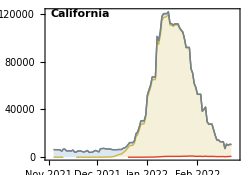
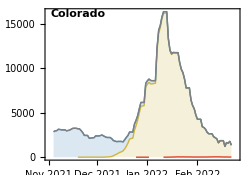
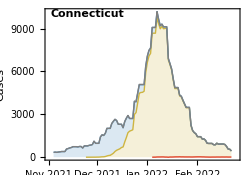
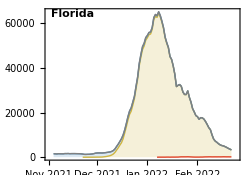
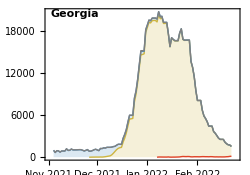
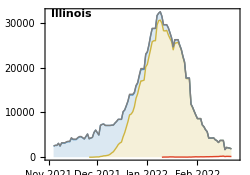
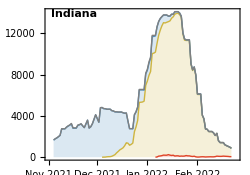
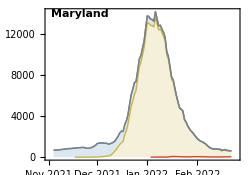
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us-split_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=500000;
```

```mathematica
splitCaseLogPlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[country_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[country_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[country,"Omicron 21L"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{50,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[4]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.88,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForCountries=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron 21L"]],"Omicron 21L",legendStartingPointY- 0.09,colors[[4]]]&,countries];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{countries,legendsForCountries}];
```

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us-split_partitioned-log-cases.png